```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
l=Flatten @Import["test2.dat"];
nn=Length[l]
```

4194304

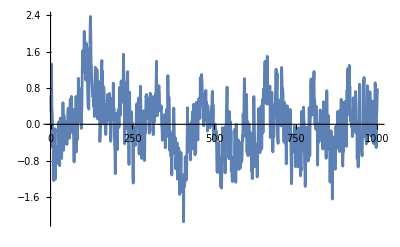

```mathematica
ListLinePlot[Take[l,UpTo[1000]]]
```

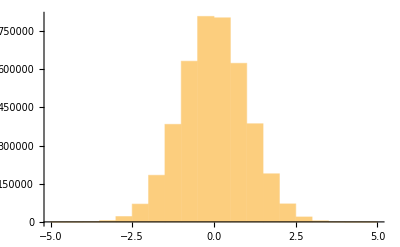

-5.69072×10^-10

1.

```mathematica
Histogram[l]
avg=Mean[l]
std=StandardDeviation[l]
```

{{0,1.},{1,0.899174},{2,0.850867},{3,0.828343},{4,0.809879},{5,0.796967},{6,0.785606},{7,0.776536},{8,0.768031},{9,0.760965},{10,0.754335},{11,0.748584},{12,0.743096},{13,0.738081},{14,0.733554},{15,0.729326},{16,0.725372},{17,0.721577},{18,0.717956},{19,0.714628},{20,0.711517},{21,0.708537},{22,0.705659},{23,0.703038},{24,0.700496},{25,0.698091},{26,0.695974},{27,0.693703},{28,0.691489},{29,0.689368},{30,0.68735},{31,0.685358},{32,0.68349},{33,0.681741},{34,0.679746},{35,0.677941},{36,0.676279},{37,0.674676},{38,0.673061},{39,0.671422},{40,0.669866},{41,0.668392},{42,0.666955},{43,0.665422},{44,0.663965},{45,0.662696},{46,0.661303},{47,0.660009},{48,0.658689},{49,0.657439},{50,0.656196},{51,0.654971},{52,0.653806},{53,0.6528},{54,0.651709},{55,0.65072},{56,0.649565},{57,0.648464},{58,0.647431},{59,0.646294},{60,0.645287},{61,0.64425},{62,0.643226},{63,0.642323},{64,0.641237},{65,0.640237},{66,0.639199},{67,0.638259},{68,0.637209},{69,0.636396},{70,0.635468},{71,0.634614},{72,0.633637},{73,0.632884},{74,0.632051},{75,0.631258},{76,0.630418},{77,0.629597},{78,0.628826},{79,0.628153},{80,0.627457},{81,0.626796},{82,0.625953},{83,0.625274},{84,0.624706},{85,0.623907},{86,0.623172},{87,0.622272},{88,0.62147},{89,0.620772},{90,0.620083},{91,0.619326},{92,0.618702},{93,0.618177},{94,0.617569},{95,0.616911},{96,0.616307},{97,0.615752},{98,0.61517},{99,0.614552},{100,0.613815}}

{a→0.895269,b→0.0611309}

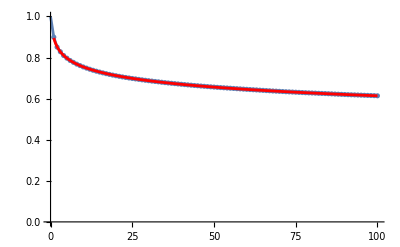

```mathematica
cf=Table[{i,CorrelationFunction[l-avg,i]},{i,0,100}]
p1=ListPlot[cf,PlotRange->{0,1},Joined->True,Mesh->All];
fnc=a-b Log[t];
sol=FindFit[Drop[cf,1],fnc,{a,b},t]
fnc=fnc/.sol;
p2=Plot[fnc,{t,1,100},PlotStyle->Red];
Show[p1,p2]
(* Logarithmic autocorrelation, see Kechner 1982 *)
```

```mathematica
tab=Table[{2^i,StandardDeviation[Map[Total,Partition[l,2^i]]]},{i,14}];
p1=ListLogLogPlot[tab];
```

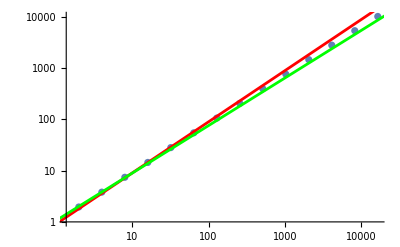

```mathematica
p2=LogLogPlot[{0.9x^(1), 1.05x^0.93},{x,1,Length[l]},PlotStyle->{Red,Green}];
Show[p1,p2]
```

```mathematica
sz=1024;
pl=Partition[l,sz];
(* power spectrum ! *)
pl=Map[(μ=Mean[#];Rest[Take[Abs[Fourier[#-μ]]^2,sz/2]])&,pl];
plavg=Mean[pl];
pft1=ListLogLogPlot[plavg,PlotRange->All,AxesLabel->{"FT amplitude","freq"},LabelStyle->Larger];
```

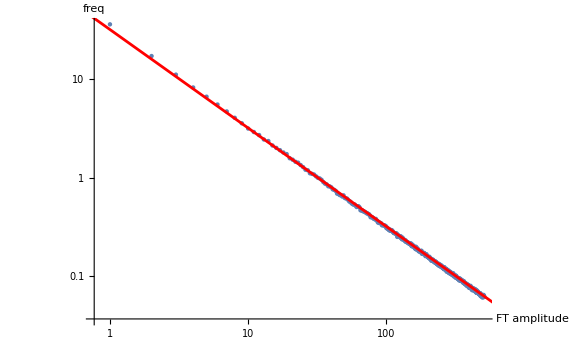

```mathematica
pft2=LogLogPlot[{32/ω},{ω,0.1,10^6},PlotStyle->{Red}];
Show[pft1,pft2,ImageSize->8 72]
```

{a→3.48765,b→1.00714}

32.709/x^1.00714

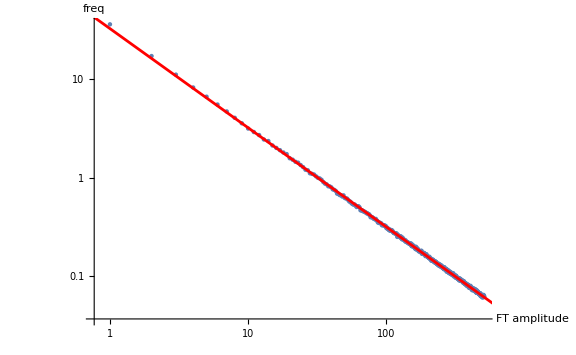

```mathematica
fnc=a-b Log[x];
sol=FindFit[Log[plavg],fnc,{a,b},x]
fnc=Exp[fnc/.sol]
pft2=LogLogPlot[fnc,{x,0.1,10^6},PlotStyle->{Red}];
Show[pft1,pft2,ImageSize->8 72]
```